```mathematica
Cparallel=3.501;
Cperp=1.574;
Rperp[x_,y_]:=((Abs[x]/1.696)^Cperp + (Abs[y]/0.6426)^Cperp)^(1/Cperp)
Rs[x_,y_,z_]:=(Rperp[x, y]^Cparallel + (Abs[z]/0.4425)^Cparallel)^(1/Cparallel)
ρBB[x_,y_,z_]:=Sech[Rs[x,y,z]]^2
```

```mathematica
ρNB[x_,y_,z_]:=(Sqrt[x^2+y^2+z^2]/0.001)^(-10)Exp[-Abs[z]/0.045]
```

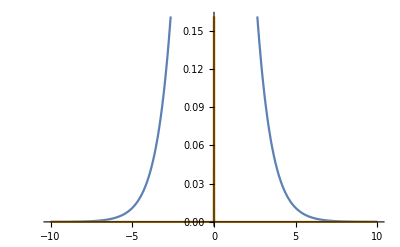

```mathematica
Plot[{ρBB[x,0,0],ρNB[x,0,0]}, {x, -10, 10}]
```